# Female mate choice

```mathematica
Clear;
```

This appendix is a script that shows the function used in the model for computing the probability of a given female to accept a potential mate. Upon evaluation of a given male, the female accepts mating with probability q, given by the piecewise function

```mathematica
q = Piecewise[{{1-y^4 p, y<0}, {p, y≥0}}]
```

Piecewise[{{1-ⅇ^(-1/2 d^2 y^2 α) y^4, y<0}, {ⅇ^(-1/2 d^2 y^2 α), y≥0}, {0, True}}]

With p defined as

```mathematica
p = Exp[-1/2 α y^2 d^2 ]
```

ⅇ^(-1/2 d^2 y^2 α)

Where y is the mating preference of the female, which defines whether mating is random (y = 0), assortative (y ≥ 0) or disassortative (y < 0), d = x_i-x_j is the distance in ecological trait space x between female i and male j being evaluated, and α is a parameter modulating the strength of mate preferences.

Mating probability is shown below as a function of difference in ecological trait values and sexual preference of the female, for different values of the mate preference strength parameter α.

```mathematica
p1 = Plot3D[ q /. {α-> 0}, {d, -2, 2}, {y, -1, 1}, PlotRange->Full, AxesLabel->{"Distance in ecological trait", "Mating preference", "Mating probability"}, ColorFunction->"BlueGreenYellow", PlotLabel->"α = 0"];
p2 = Plot3D[ q /. {α-> 1}, {d, -2, 2}, {y, -1, 1}, PlotRange->Full, AxesLabel->{"Distance in ecological trait", "Mating preference", "Mating probability"}, ColorFunction->"BlueGreenYellow", PlotLabel->"α = 1"];
p3 = Plot3D[ q /. {α-> 10}, {d, -2, 2}, {y, -1, 1}, PlotRange->Full, AxesLabel->{"Distance in ecological trait", "Mating preference", "Mating probability"}, ColorFunction->"BlueGreenYellow", PlotLabel->"α = 10"];
p4 = Plot3D[ q /. {α-> 100}, {d, -2, 2}, {y, -1, 1}, PlotRange->Full, AxesLabel->{"Distance in ecological trait", "Mating preference", "Mating probability"}, ColorFunction->"BlueGreenYellow", PlotLabel->"α = 100"];
```

```mathematica
p3
```

-Graphics3D-

```mathematica
Export["/home/raphael/mating_prob_alpha1.png",p2,"PNG", ImageResolution->300]
Export["/home/raphael/mating_prob_alpha10.png",p3,"PNG", ImageResolution->300]
```

/home/raphael/mating_prob_alpha1.png

/home/raphael/mating_prob_alpha10.png

```mathematica
GraphicsGrid[{{p1, p2}, {p3, p4}}, ImageSize->1000]
```

-Graphics-

Note that parameter α gives the function a somewhat problematic behavior when small. α controls the width of the range of (dis)favored male phenotypes by the female, such that when α is high, the female expresses stronger discrimination among males with different phenotypes. The function has the desired characteristics when α is high (α > 1). For small values of α, the female's discrimination disappears and preference flattens out across the range of male phenotypes, which is as wanted. Except that for such small values, the baseline mating probability across male phenotypes is smaller for disassortative mating than for assortative mating. As a consequence, when α goes to zero, the mating probability just depends on the sexual preference of the female, y, and goes to zero as y becomes more negative (disassortative mating), while staying at one when y > 0 (assortative mating). In other words, when α is small, females do not discriminate between males, yet females with disassortative preferences will reject some males they encounter with probability y^4 (therefore rejecting all males if y = 0), while females with assortative preferences will systematically accept all the males they encounter and therefore have more offspring, which will induce some selection in favor of assortative mating even in the absence of discrimination among males, which is not what we want...

```mathematica
q= Piecewise[{{1-y^(d^2), y≤0}, {(1-y)^(d^2), y>0}}]
```

Piecewise[{{1-y^(d^2), y≤0}, {(1-y)^(d^2), y>0}, {0, True}}]

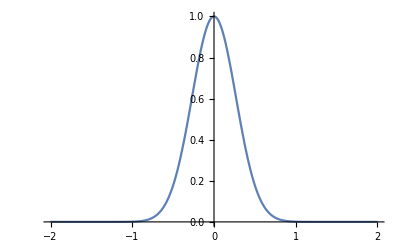

```mathematica
Plot[q/.y->0.999, {d, -2, 2}, PlotRange->{0,1}]
```

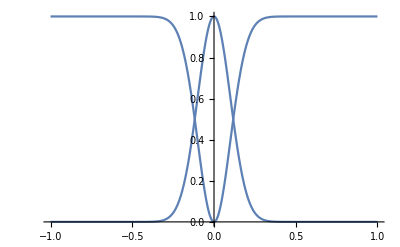

```mathematica
A[d_]:=Exp[-1/2 d^2/Subscript[σ, m]^2];
B[d_]:=1-Exp[-1/2 d^2/Subscript[σ, m]^2];
Plot[{A[d],B[d]}/.Subscript[σ, m]->0.1, {d,-1,1}, PlotRange->{0,1}]
```

```mathematica
M[d_,y_]:=y A[d] + (1-y)B[d];
Plot3D[M[d, y]/.Subscript[σ, m]->0.1, {d, -1, 1}, {y, 0, 1}]
```

```mathematica
-Graphics3D-0.2
```

```mathematica
Integrate[M[d,y]/.y->0.4/.Subscript[σ, m]->0.1, {d, -2,2}]
```

2.34987

```mathematica
G[d_,y_]:=1-y+(2 y -1)A[d];
M[d_,y_]:=G[d,y]/(0.5+Abs[y-0.5]);
A[d_]:=Exp[-α d^2 ];
Plot3D[M[d, y]/.α->10, {d, -1, 1}, {y, 0, 1}]
Plot3D[G[d, y]/.α->10, {d, -1, 1}, {y, 0, 1}]
```

-Graphics3D-

-Graphics3D-